## 1.1

```mathematica
Clear["Global`*"]
```

```mathematica
ages = {14, 15, 16, 16, 16, 22, 22, 24, 24, 25, 25, 25, 25, 25}
```

{14,15,16,16,16,22,22,24,24,25,25,25,25,25}

```mathematica
TotalCount = Length[ages];
p[j_]:= Count[ages, j]/TotalCount
Average=Sum[i*p[i], {i, Min[ages], Max[ages]}] ;
```

### (a) Computer <j*2> and <j>*2

```mathematica
AverageOfSquares = N[Sum[j^2 * p[j], {j, Min[ages], Max[ages]}],6]
SquaredAverage = Average^2
```

459.571

441

### (b) Determine Δj for each j, use 1.11 to determine std deviation

```mathematica
spread[j_] := j - Average
Map[spread, ages]
```

{-7,-6,-5,-5,-5,1,1,3,3,4,4,4,4,4}

```mathematica
sigma= Sqrt[Sum[ p[j]* spread[j]^2, {j,Min[ages], Max[ages]}] ];
N[sigma, 5]
```

4.3095

### (c) Use results in (a) and (b) to check equation 1.12

```mathematica
sigma2 = Sqrt[AverageOfSquares - SquaredAverage];
N[sigma2, 5]
```

4.309

## Problem 1.2

```mathematica
Clear["Global`*"]
```

### (a) Find standard deviation

```mathematica
$Assumptions=h>0;
p[x_]:=1/(2 √(h x))
Simplify[∫_0^h p[x]ⅆx,h>0];
average=Simplify[∫_0^h x p[x]ⅆx,h>0];
averageOfSquares=∫_0^h x^2 p[x]ⅆx;
averageSquared=average^2;
sigma=Simplify[√(averageOfSquares-averageSquared)]
```

(2 h)/(3 √5)

### (b) What is probability that photograph is outside of 1 standard deviation

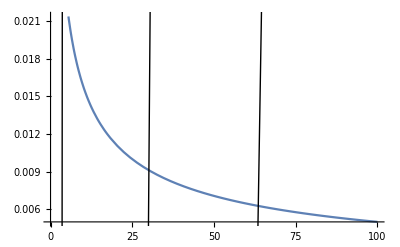

```mathematica
Block[{h=100}, Plot[p[x], {x, 0, h},Epilog->{
InfiniteLine[{ average + sigma,0},{ average + sigma,1}],
InfiniteLine[{ sigma,0},{sigma,1}],InfiniteLine[{average - sigma,0},{average-sigma,1}]}]]
```

```mathematica
outside1Sigma =Simplify[∫_0^(average-sigma) p[x]ⅆx + ∫_(average + sigma)^h p[x]ⅆx];
N[outside1Sigma,3]
```

0.393

## 1.3

```mathematica
Clear["Global`*"]
```

### (a) Use Equation 1.16 to determine A

```mathematica
$Assumptions = {A>0, a>0,λ>0};
p[x_]:=A ⅇ^(-λ(x-a)^2);
Solve[Integrate[p[x], {x, - ∞, ∞}] == 1, A]
```

{{A→(√λ)/(√π)}}

```mathematica
{{A->(√λ)/(√π)}}
A->(√λ)/(√π)
p[x]
```

{{A→(√λ)/(√π)}}

```mathematica
A=(√λ)/(√π);
average = Integrate[x*p[x], {x, - ∞, ∞}];
averageOfSquares = Integrate[x*x*p[x], {x, -∞, ∞}];
sigma = Simplify[Sqrt[averageOfSquares - average^2]]
```

1/(√2 √λ)

#### Plot

(ⅇ^(-(-a+x)^2 λ) √λ)/(√π)

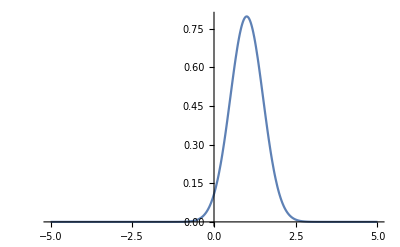

```mathematica
p[x]
Block[{a=1, λ=2},Plot[p[x], {x, -5, 5}, PlotRange->Full]]
```